# Non-dimensionalized axisymmetric Navier-Stokes in ALE with particle tracking

## Incompressible fluid

Copyright: Francesco Costanzo
Date: 4 May 2017

## Notebook Initialization

## Clearing Local Definitions

```mathematica
If[Length[Names[Evaluate[Context[]<>"*"]]]≠0,(ClearAll[Evaluate[Context[]<>"*"]];Remove[Evaluate[Context[]<>"*"]];)]
```

## Auxiliary Elements: Units Package and Significant Digits Function

### Units Package

The Units package provides declarations for a wide number of units in addition to providing a number of conversion factors.

```mathematica
<<Units`
```

The Convert function in the Units package is not listable.  Hence, to convert units in lists representing vector quantitities, we define the following function:

```mathematica
ListConvert[xx_?ListQ,y_]:=Convert[#,y]&/@xx;
```

### Significant Digits Function

The function below allows one to evaluate a number to a specified number of significant digits.  The function accepts two arguments.  The first is any Mathematica expression that may or may not contain numbers.  The second is an integer specifing the number of significant digits.

```mathematica
SF[xx_,n_?IntegerQ]:=xx/.Map[(Level[xx,{0,Infinity}][[#]]->SFN[Level[xx,{0,Infinity}][[#]],n])&,Flatten[Position[Map[((Head[#]===Real)||(Head[#]===Complex))&,Level[xx,{0,Infinity}]],True]]];
SFN[xx_Complex,n_?IntegerQ]:=If[Head[xx]==Complex,SFN[Re[xx],n]+I SFN[Im[xx],n],SFN[xx,n]];
SFN[xx_,n_?IntegerQ]:=Module[{digits,DecimalPointLocation,x,signx},
If[NumberQ[xx],
signx=Sign[x];
x=xx*1.0;
If[x==0,N[0],
digits=(RealDigits[x])[[1]];
DecimalPointLocation=(RealDigits[x])[[2]];
If[digits[[n+1]]>5,digits[[n]]=digits[[n]]+1];
If[(digits[[n+1]]==5 &&Norm[Drop[digits,n+1]]==0),If[OddQ[digits[[n]]],digits[[n]]=digits[[n]]+1]];
If[(digits[[n+1]]==5 &&Norm[Drop[digits,n+1]]>0),digits[[n]]=digits[[n]]+1];
digits=Take[digits,n];
signx N[FromDigits[{digits,DecimalPointLocation},10],n]],xx]
];
```

## Auxiliary Algebraic Operators

```mathematica
Sym[A_]:=1/2(A+Transpose@A);
Skw[A_]:=1/2(A-Transpose@A);
Sph[A_]:=If[MatrixQ[A]&&Dimensions[A][[1]]==Dimensions[A][[2]],1/3 Tr[A]IdentityMatrix[Dimensions[A][[1]]],Print["Incorrect Argument!"]];
Dev[A_]:=A-Sph[A];
```

## Differential Operators: Gradient, Divergence, and Laplacian

```mathematica
ProblemSettings=<|"Formulation"->"3D","ComponentNaming"->"Numeric","Coordinates"->{x,y,z},"CSystem"->"Cartesian","TDependent"->True|>;
```

### Premise

Only two coordinate systems are allowed: Cartesian and cylindrical. The dimension is understood to be 3 in all cases. The symbols for the two coordinate systems are chosen by the user.  However, for the cylindrical coordinate system, the first coordinate must be the radial coordinate and the second coordinate must be the angular coordinate.

### Gradient

```mathematica
ClearAll[DOGrad];
DOGrad::usage="DOGrad[a,ProblemSettings] returns the gradient of a.  ProblemSettings is an association that specifies, among other things the symbols used for coordinates and the type of coordinate system used.";
DOGrad::invargProblemSettings="The problem settings provided are invalid. Here is an example of a properly formatted ProblemSettings association:
ProblemSettings=<|\"Formulation\"→\"3D\",\"ComponentNaming\"→\"Numeric\",\"Coordinates\"→{x,y,z},\"CSystem\"→\"Cartesian\",\"TDependent\"→True|>;";
DOGrad::invCoordinateSystem="The selected coordinate system is invalid.";
DOGrad::invCoordinates="It is assumed that the coordinates are for a threedimensional physical context. Invalid number of coordinate names provided.";
DOGrad[a_,ProblemSetup_]:=Module[{Coordinates,CoordType,d,ξ,η,ζ,Da,id,i,j,target,temp,sign},
(* Check that the ProblemSetup information is valid. *)
If[!AssociationQ@ProblemSetup,
Message@DOGrad::invargProblemSettings;
Return@$Failed;
];
Coordinates=ProblemSetup["Coordinates"];
CoordType=ProblemSetup["CSystem"];
If[CoordType≠"Cartesian"&&CoordType≠"Cylindrical",
Message@DOGrad::invCoordinateSystem;
Return@$Failed;
];
If[Length@Coordinates≠3,
Message@DOGrad::invCoordinates;
Return@$Failed;
];
ξ=Coordinates[[1]];
η=Coordinates[[2]];
ζ=Coordinates[[3]];
d=Length@Dimensions@a;
If[!ListQ@a,d=0];
If[CoordType=="Cartesian",
Return@Map[{D[#, ξ],D[#, η],D[#, ζ]}&,a,{d}];
];
Da=Map[{D[#, ξ],1/ξ D[#, η],D[#, ζ]}&,a,{d}];
id=Tuples[{1,2,3},{d}];
If[Length[id]==1,Return[Da]];
id=Drop[id,-1];
Do[
temp=Extract[a,id[[i]]]/ξ;
Do[
sign=0;
If[id[[i,j]]==1,
target=Append[ReplacePart[id[[i]],j->2],2];sign=1];
If[id[[i,j]]==2,
target=Append[ReplacePart[id[[i]],j->1],2];
sign=-1;];
If[sign≠0,
Da=ReplacePart[Da,target->Extract[Da,target]+sign*temp]];
,{j,Length[id[[i]]]}];
,{i,Length[id]}];
Return[Da];
];
Protect[DOGrad];
```

```mathematica
example=<|"Formulation"->"3D","ComponentNaming"->"Numeric","Coordinates"->{x,y,z},"CSystem"->"Cartesian","TDependent"->True|>
```

<|Formulation→3D,ComponentNaming→Numeric,Coordinates→{x,y,z},CSystem→Cartesian,TDependent→True|>

```mathematica
DOGrad[Sin[x],example]
```

{Cos[x],0,0}

### Divergence

```mathematica
ClearAll[DODiv];
DODiv::usage="DODiv[a,ProblemSettings] returns the divergence of a.  ProblemSettings is an association that specifies, among other things the symbols used for coordinates and the type of coordinate system used.";
DODiv::invarga="The first argument is invalid: there is no such thing as the divergence of a scalar.";
DODiv::invargProblemSettings="The problem settings provided are invalid. Here is an example of a properly formatted ProblemSettings association:
ProblemSettings=<|\"Formulation\"→\"3D\",\"ComponentNaming\"→\"Numeric\",\"Coordinates\"→{x,y,z},\"CSystem\"→\"Cartesian\",\"TDependent\"→True|>;";
DODiv::invCoordinateSystem="The selected coordinate system is invalid. The only allowed coordinate systems are the Cartesian and Cylindrical ones.";
DODiv::invCoordinates="It is assumed that the coordinates are for a threedimensional physical context. Invalid number of coordinate names provided.";
DODiv[a_,ProblemSetup_]:=Module[{Coordinates,CoordType,d,ξ,η,ζ,Diva,ξlist,ηlist,ζlist,source,sourcevalue,target,innertarget,sign,i,j},
If[!ListQ[a],
Message@DODiv::invarga;
Return[$Failed];
];
(* Check that the ProblemSetup information is valid. *)
If[!AssociationQ@ProblemSetup,
Message@DODiv::invargProblemSettings;
Return@$Failed;
];
Coordinates=ProblemSetup["Coordinates"];
CoordType=ProblemSetup["CSystem"];
If[CoordType≠"Cartesian"&&CoordType≠"Cylindrical",
Message@DODiv::invCoordinateSystem;
Return@$Failed;
];
If[Length@Coordinates≠3,
Message@DODiv::invCoordinates;
Return@$Failed;
];
ξ=Coordinates[[1]];
η=Coordinates[[2]];
ζ=Coordinates[[3]];
d=Length@Dimensions@a;
If[d==1&&CoordType=="Cartesian",Return[D[a[[1]], ξ]+D[a[[2]], η]+D[a[[3]], ζ]]];
If[d==1,Return[D[a[[1]], ξ]+(D[a[[2]], η]+a[[1]])/ξ+D[a[[3]], ζ]]];
Diva=ConstantArray[0,Drop[Dimensions[a],-1]];
d-=1;
ξlist=Tuples[Join[Table[{1,2,3},{d}],{{1}}]];
ηlist=Tuples[Join[Table[{1,2,3},{d}],{{2}}]];
ζlist=Tuples[Join[Table[{1,2,3},{d}],{{3}}]];
If[CoordType=="Cylindrical",
Do[
source=ξlist[[i]];
sourcevalue=Extract[a,source];
target =Drop[source,-1];
Diva=ReplacePart[Diva,target->Extract[Diva,target]+sourcevalue/ξ+D[sourcevalue, ξ]];,
{i,Length[ξlist]}
];
Do[
source=ηlist[[i]];
target =Drop[source,-1];
Diva=ReplacePart[Diva,target->Extract[Diva,target]+1/ξ D[Extract[a,source], η]];
Do[
sign=0;
If[target[[j]]==1,sign=1;innertarget=ReplacePart[target,j->2];];
If[target[[j]]==2,sign=-1;innertarget=ReplacePart[target,j->1];];
If[sign≠0,
Diva=ReplacePart[Diva,innertarget->Extract[Diva,innertarget]+sign/ξ Extract[a,source]]];
,{j,Length[target]}
];
,
{i,Length[ηlist]}
];
Do[
source=ζlist[[i]];
target =Drop[source,-1];
Diva=ReplacePart[Diva,target->Extract[Diva,target]+D[Extract[a,source], ζ]];,
{i,Length[ζlist]}
];
Return[Diva];
];
Do[
source=ξlist[[i]];
target =Drop[source,-1];
Diva=ReplacePart[Diva,target->Extract[Diva,target]+D[Extract[a,source], ξ]];,
{i,Length[ξlist]}
];
Do[
source=ηlist[[i]];
target =Drop[source,-1];
Diva=ReplacePart[Diva,target->Extract[Diva,target]+D[Extract[a,source], η]];,
{i,Length[ηlist]}
];
Do[
source=ζlist[[i]];
target =Drop[source,-1];
Diva=ReplacePart[Diva,target->Extract[Diva,target]+D[Extract[a,source], ζ]];,
{i,Length[ζlist]}
];
Return[Diva];
];
Protect[DODiv];
```

### Laplacian

```mathematica
ClearAll[DOLaplacian];
DOLaplacian::usage="DOLaplacian[a,ProblemSettings] returns the laplacian of a.  ProblemSettings is an association that specifies, among other things the symbols used for coordinates and the type of coordinate system used.";
DOLaplacian::invargProblemSettings="The problem settings provided are invalid. Here is an example of a properly formatted ProblemSettings association:
ProblemSettings=<|\"Formulation\"→\"3D\",\"ComponentNaming\"→\"Numeric\",\"Coordinates\"→{x,y,z},\"CSystem\"→\"Cartesian\",\"TDependent\"→True|>;";
DOLaplacian::invCoordinateSystem="The selected coordinate system is invalid.";
DOLaplacian::invCoordinates="It is assumed that the coordinates are for a threedimensional physical context. Invalid number of coordinate names provided.";
DOLaplacian[a_,ProblemSetup_]:=Module[
{Coordinates,CoordType},
(* Check that the ProblemSetup information is valid. *)
If[!AssociationQ@ProblemSetup,
Message@DOLaplacian::invargProblemSettings;
Return@$Failed;
];
Coordinates=ProblemSetup["Coordinates"];
CoordType=ProblemSetup["CSystem"];
If[CoordType≠"Cartesian"&&CoordType≠"Cylindrical",
Message@DOLaplacian::invCoordinateSystem;
Return@$Failed;
];
If[Length@Coordinates≠3,
Message@DOLaplacian::invCoordinates;
Return@$Failed;
];
Return@DODiv[DOGrad[a,ProblemSetup],ProblemSetup];
];
Protect[DOLaplacian];
```

### Tensor Derivative

```mathematica
ClearAll[TDerivative];
TDerivative[f_,t_]:=Module[{},
MapThread[D[f,#] &, {t}, Depth[t]-1]
];
Protect[TDerivative];
```

## Generalized Inner Product

```mathematica
IP::usage="IP[a,b] returns the inner product of a and b as long as a and b are members of the same vector space.";
IP::invargs="The operands are incompatible.";
IP[A_,B_]:=Module[{},
If[(!ListQ@A)&&(!ListQ@B),
Return@Total@Flatten@MapThread[Times,{{A},{B}}];
];
If[ListQ@A&&ListQ@B&&Dimensions@A==Dimensions@B,
Return@Total@Flatten@MapThread[Times,{A,B}];,
Message[IP::invargs];
Return[$Failed];
];
];
Protect[IP];
```

## Field Instantiation Functions

### Core function for the instantiation of a field

```mathematica
ClearAll[FieldInstantiationCore];
FieldInstantiationCore::usage="FieldInstantiationCore[FieldDeclaration,ProblemSettings] instantiantes a field whose properties are specified in the \"FieldDeclaration\". The argument \"ProblemSettings\" is an association with information pertaining to the problem as a whole.
A \"FieldDeclaration\" is a triple: {A, B, C}:
A: the name of the field as a string.
B: a nonnegative integer indicating the tensor rank of the field.
C: an association with pertinent properties for the field.
";
FieldInstantiationCore::invarg1="The first argument must be a field declaration (a list).";
FieldInstantiationCore::invarg2="The second argument must be an association.";
FieldInstantiationCore::invarg3="Invalid field declaration: declaration has incorrect length.";
FieldInstantiationCore::invarg4="Invalid field declaration: field name is not a string.";
FieldInstantiationCore::invarg5="Invalid field declaration: invalid tensor rank.";
FieldInstantiationCore::invarg6="Invalid field declaration: field properties are not an association.";
FieldInstantiationCore::invfieldproperties="Unrecognized properties specifications for field `1`.";
FieldInstantiationCore::warning1="Invalid symmetrization request for field `1`: proceeding without symmetrization.";
FieldInstantiationCore[f_,ProblemSetup_]:=Module[
{
name,
rank,
properties,
keys,
nconvention,
coordinates,
coordsystem,
userproperties,
userkeys,
α,
β,
γ,
ξ,
η,
ζ,
cc,
rcoords,
sf,
symbols,
temp,
dv,
indices,
ids,
subid,
subidv,
source,
target,
sign,
i,
j,
fexpression,
Tfexpression,
rules,
output
},
(* Check that are arguments are of the right type. *)
If[!ListQ@f,
Message@FieldInstantiationCore::invarg1;
Return@$Failed;
];
If[!AssociationQ@ProblemSetup,
Message@FieldInstantiationCore::invarg2;
Return@$Failed;
];

(* Check that the field declaration list is acceptable. *)
If[(Length@f<2)||(Length@f>3),
Message@FieldInstantiationCore::invarg3;
Return@$Failed;
];
If[!StringQ@f[[1]],
Message@FieldInstantiationCore::invarg4;
Return@$Failed;
];
If[!(IntegerQ@f[[2]]&&f[[2]]≥0),
Message@FieldInstantiationCore::invarg5;
Return@$Failed;
];
If[Length@f==3,
If[!AssociationQ@f[[3]],
Message@FieldInstantiationCore::invarg6;
Return@$Failed;
];
];

(* Set up the default properties association. *)
properties=<|
"Principal Unknown"->False,
"Vector: 2D Formulation Constant Value"->0,
"Tensor: 2D Formulation Default Constant Value"->0,
"Tensor: 2D Formulation Address-Value List"->{},
"Symmetry"->"None"
|>;
keys=Keys@properties;
(* Process the declaration. *)
name=f[[1]];
rank=f[[2]];
If[Length@f==3,
userproperties=f[[3]];,
userproperties=<||>;
];
userkeys=Keys@userproperties;
If[Length@Union[keys,userkeys]>Length@keys,
Message[FieldInstantiationCore::invfieldproperties,name];
Return[$Failed];
];
If[Length@Intersection[userkeys,keys]>0,
(properties[#]=userproperties[#])&/@Intersection[userkeys,keys];
];

(* Set the naming convention, coordinates and the coordinate system. *)
nconvention=ProblemSetup["ComponentNaming"];
coordinates=ProblemSetup["Coordinates"];
coordsystem=ProblemSetup["CSystem"];
(* Set coordinates in use. *)
ξ=ToString@coordinates[[1]];
η=ToString@coordinates[[2]];
ζ=ToString@coordinates[[3]];
(* Set the component indices. *)
If[rank>0,
If[nconvention=="Coordinates",
α=ξ;β=η;γ=ζ;,
α="1";β="2";γ="3";
];
];


(* Proceed to instantiate the field and record the generated symbol. *)
(* Begin with checking whether or not the symbol exsists and clear it. *)
If[NameQ@Evaluate@name,Remove@Evaluate@name;];
fexpression=ToExpression@ArrayReshape[name<>#&/@Tuples[{α,β,γ},rank],Table[3,{i,rank}]];
output={{name,Evaluate[ToExpression@name]=fexpression}};
symbols={name};

(* Is this field is a principal unknown field then generate corresponding *)
(* 1. test functions;                                      *)
(* 2. gradients;                                           *)
(* 3. gradients of test functions.                         *)
(* 4. time rates for time dependent problems.              *)
(* 5. second order time rates for time dependent problems. *)

(* Generate the test functions. *)
If[properties["Principal Unknown"],
temp="T"<>name;
If[NameQ@Evaluate@temp,Remove@Evaluate@temp;];
fexpression=ToExpression@StringReplace[ToString@output[[1,2]],name->temp];
output=Join[output,{{temp,Evaluate[ToExpression@temp]=fexpression}}];
symbols=Join[symbols,{temp}];
];

(* Generate the gradients. *)
sf=Map[ToString,output[[1,2]],{rank}];
If[properties["Principal Unknown"]&& coordsystem=="Cartesian",
temp="D"<>name;
If[NameQ@Evaluate@temp,Remove@Evaluate@temp;];
fexpression=ToExpression[Map[{#<>ξ,#<>η,#<>ζ}&,sf,{rank}]];
output=Join[output,{{temp,Evaluate[ToExpression@temp]=fexpression}}];
symbols=Join[symbols,{temp}];
temp="TD"<>name;
If[NameQ@Evaluate@temp,Remove@Evaluate@temp;];
fexpression=ToExpression[Map[{"T"<>#<>ξ,"T"<>#<>η,"T"<>#<>ζ}&,sf,{rank}]];
output=Join[output,{{temp,Evaluate[ToExpression@temp]=fexpression}}];
symbols=Join[symbols,{temp}];
];

If[properties["Principal Unknown"]&& coordsystem=="Cylindrical",
temp="D"<>name;
If[NameQ@Evaluate@temp,Remove@Evaluate@temp;];
temp="TD"<>name;
If[NameQ@Evaluate@temp,Remove@Evaluate@temp;];
fexpression=ToExpression[Map[{#<>ξ,#<>η<>"/"<>ξ,#<>ζ}&,sf,{rank}]];
Tfexpression=ToExpression[Map[{"T"<>#<>ξ,"T"<>#<>η<>"/"<>ξ,"T"<>#<>ζ}&,sf,{rank}]];
If[rank>0,
ids=Drop[Tuples[{1,2,3},{rank}],-1];
Do[
temp=Extract[output[[1,2]],ids[[i]]]/ToExpression[ξ];
Do[
sign=0;
If[ids[[i,j]]==1,
target=Append[ReplacePart[ids[[i]],j->2],2];sign=1];
If[ids[[i,j]]==2,
target=Append[ReplacePart[ids[[i]],j->1],2];
sign=-1;];
If[sign≠0,
fexpression=ReplacePart[fexpression,target->Extract[fexpression,target]+sign*temp]];
,{j,Length[ids[[i]]]}];
,{i,Length[ids]}];
Do[
temp=Extract[output[[2,2]],ids[[i]]]/ToExpression[ξ];
Do[
sign=0;
If[ids[[i,j]]==1,
target=Append[ReplacePart[ids[[i]],j->2],2];sign=1];
If[ids[[i,j]]==2,
target=Append[ReplacePart[ids[[i]],j->1],2];
sign=-1;];
If[sign≠0,
Tfexpression=ReplacePart[Tfexpression,target->Extract[Tfexpression,target]+sign*temp]];
,{j,Length[ids[[i]]]}];
,{i,Length[ids]}];
];
temp="D"<>name;
output=Join[output,{{temp,Evaluate[ToExpression@temp]=fexpression}}];
symbols=Join[symbols,{temp}];
temp="TD"<>name;
output=Join[output,{{temp,Evaluate[ToExpression@temp]=Tfexpression}}];
symbols=Join[symbols,{temp}];
]; (* End if Cylindrical *)

(* Deal with the time rates. *)
If[properties["Principal Unknown"]&& ProblemSetup["TDependent"],
temp=name<>"t";
If[NameQ@Evaluate@temp,Remove@Evaluate@temp;];
(* Set names for the coordinates in use. *)
sf=Map[ToString,output[[1,2]],{rank}];
fexpression=ToExpression[Map[(#<>"t")&,sf,{rank}]];
output=Join[output,{{temp,Evaluate[ToExpression@temp]=fexpression}}];
symbols=Join[symbols,{temp}];
temp=name<>"tt";
If[NameQ@Evaluate@temp,Remove@Evaluate@temp;];
fexpression=ToExpression[Map[(#<>"tt")&,sf,{rank}]];
output=Join[output,{{temp,Evaluate[ToExpression@temp]=fexpression}}];
symbols=Join[symbols,{temp}];
];

(* ------------------------------------------------------ *)
(* ------------------------------------------------------ *)

(* Now generate the replacement rules for the field. *)
(* Initialize the Rules list. *)
rules={};

(* Enforce symmetry. *)
If[properties["Symmetry"]≠"None"&& rank<2,
Message[FieldInstantiationCore::warning1,name];
properties["Symmetry"]="None";
];

If[properties["Symmetry"]=="Symmetric",
(* Switch to numeric indices for addressing purposes. *)
indices=Tuples[{1,2,3},{rank}];
While[Length[indices]>0 ,
ids=Permutations[indices[[1]]];
If[Length[ids]==1,indices=Drop[indices,1],
source=ids[[1]];
rules=Join[rules,(ToString[Extract[output[[1,2]],#]->Extract[output[[1,2]],source]])&/@Drop[ids,1]];
If[properties["Principal Unknown"],
rules=Join[rules,(ToString[Extract[output[[2,2]],#]-> Extract[output[[2,2]],source]])&/@Drop[ids,1]];
rules=Join[rules,(ToString@Thread[Extract[output[[3,2]],#]-> Extract[output[[3,2]],source]])&/@Drop[ids,1]];
rules=Join[rules,(ToString@Thread[Extract[output[[4,2]],#]-> Extract[output[[4,2]],source]])&/@Drop[ids,1]];
If[ ProblemSetup["TDependent"],
rules=Join[rules,(ToString[Extract[output[[5,2]],#]->Extract[output[[5,2]],source]])&/@Drop[ids,1]];
rules=Join[rules,(ToString[Extract[output[[6,2]],#]->Extract[output[[6,2]],source]])&/@Drop[ids,1]];
];
];
indices=Delete[indices,Flatten[Position[indices,#]&/@ids,1]]
];
];
];

If[properties["Symmetry"]=="Skewsymmetric",
(* Switch to numeric indices for addressing purposes. *)
indices=Tuples[{1,2,3},{rank}];
While[Length[indices]>0 ,
ids=Permutations[indices[[1]]];
source=ids[[1]];
rules=Join[rules,(ToString[Extract[output[[1,2]],#]->Signature[#]Extract[output[[1,2]],source]])&/@Drop[ids,1]];
If[properties["Principal Unknown"],
rules=Join[rules,(ToString[Extract[output[[2,2]],#]->Signature[#] Extract[output[[2,2]],source]])&/@Drop[ids,1]];
rules=Join[rules,(ToString@Thread[Extract[output[[3,2]],#]->Signature[#]Extract[output[[3,2]],source]])&/@Drop[ids,1]];
rules=Join[rules,(ToString@Thread[Extract[output[[4,2]],#]-> Signature[#]Extract[output[[4,2]],source]])&/@Drop[ids,1]];
If[ ProblemSetup["TDependent"],
rules=Join[rules,(ToString[Extract[output[[5,2]],#]->Signature[#]Extract[output[[5,2]],source]])&/@Drop[ids,1]];
rules=Join[rules,(ToString[Extract[output[[6,2]],#]->Signature[#]Extract[output[[6,2]],source]])&/@Drop[ids,1]];
];
];
indices=Delete[indices,Flatten[Position[indices,#]&/@ids,1]];
];
];

(* If the formulation is 3D there is nothing to do. *)
If[ProblemSetup["Formulation"]=="3D",
Return[{symbols,output,rules}];
];

(* Now produce the replacement rules for the components of the field with special values. *)
(* Identify which root component of the formulation is constant. *)
cc=2;
If[ProblemSetup["Formulation"]=="Plane",cc=3;];
rcoords=Drop[{ξ,η,ζ},{cc}];
(* If the field is not a scalar, deal with its components. *)
If[rank>0,
ids=Tuples[{1,2,3},{rank}];
ids=Extract[ids,Position[ContainsAny[#,{cc}]&/@ids,True]];
(* Suppose that the field is a vector field. *)
If[rank==1 ,
(* Default value of the constant component of the field is zero. *)
temp=properties["Vector: 2D Formulation Constant Value"];
(* Set the selected component equal to its corresponding constant value. *)
rules=Join[rules,{ToString@output[[1,2]][[cc]]<>"->"<>ToString[temp]}];
];
(* Suppose that the field is of tensorial order higher than 1. *)
If[rank>1,
(* Again, set the default value. *)
dv=properties["Tensor: 2D Formulation Default Constant Value"];
(* Compile the list of components for which non-default values are prescribed. *)
subid=#[[1]]&/@properties["Tensor: 2D Formulation Address-Value List"];
subidv=#[[2]]&/@properties["Tensor: 2D Formulation Address-Value List"];
(* Let id be the addresses of those components that have the default value. *)
ids=Complement[ids,Flatten[Permutations[#]&/@subid,1]];
(* Identify the symbols of the components with default values and create the associated rules. *)
temp=Variables@Level[Extract[output[[1,2]],#]&/@ids,{-1}];
rules=Join[rules,(ToString[#]<>"->"<>ToString[dv])&/@temp];
(* Identify the symbols with non-default values and set the corresponding rules. *)
temp=Variables@Level[Extract[output[[1,2]],#]&/@subid,{-1}];
temp=Transpose[{temp,subidv}];
rules=Join[rules,(ToString[#[[1]]]<>"->"<>ToString[#[[2]]])&/@temp];
];
];
(* Eliminate duplicate rules, if any. *)
rules=Union@Flatten@rules;

(* Now that all the rules for all constant fields have been set, *)(* if the field is a principal unknown, create the rules for the *)
(* corresponding test functions, gradients, and time derivatives. *)
If[properties["Principal Unknown"],
(* Next, find the symbols whose values are being set to a constant by the rules. *)
temp=DeleteCases[If[NumberQ@#[[2]],ToString@#[[1]]]&/@ToExpression@rules,Null];
(* Set the test functions for these symbols to zero. *)
rules=Join[rules,("T"<>#<>"->0")&/@temp];
(* Set the test time rates for these symbols to zero. *)
rules=Join[rules,{#<>"t"<>"->0",#<>"tt"<>"->0"}&/@temp];
(* Set any derivative of these functions and their test functions to zero. *)
rules=Join[rules,{#<>rcoords[[1]]<>"->0",#<>rcoords[[2]]<>"->0"}&/@temp];
rules=Join[rules,{"T"<>#<>rcoords[[1]]<>"->0","T"<>#<>rcoords[[2]]<>"->0"}&/@temp];
(* Now add the rules concerning the derivatives with respect to the constant direction. *)
If[rank>0,
temp=ToString[#]&/@Variables@Flatten[output[[1,2]]];
rules=Join[rules,(#<>ToString[coordinates[[cc]]]<>"->0")&/@temp];
rules=Join[rules,("T"<>#<>ToString[coordinates[[cc]]]<>"->0")&/@temp];
];
If[rank==0,
rules=Join[rules,{name<>ToString[coordinates[[cc]]]<>"->0","T"<>name<>ToString[coordinates[[cc]]]<>"->0"}];
];
];
rules=Union@ToExpression@Flatten@rules;
(* Export the results. *)
Return[{symbols,output,rules}];
];
Protect[FieldInstantiationCore];
```

### Instantiation of field(s)

```mathematica
ClearAll[FieldsInstantiation];
FieldsInstantiation::usage="Provide instructions here";
FieldsInstantiation::invarg1="No field declaration or no field declaration list provided.";
FieldsInstantiation::invarg2="Invalid problem settings: these are provided via an association.";
FieldsInstantiation[f_,ProblemSetup_]:=
With[{frules:=FormulationRules},
Module[
{nf,fl,totaloutcome,symbols,rules,resetkeys,lFormulationRules},
(* Determine the number of fields to instantiate. *)
If[!ListQ@f,
Message@FieldsInstantiation::invarg1;
Return[$Failed];
];
nf=Length@f;
fl=f;
If[nf==0,
Message@FieldsInstantiation::invarg1;
Return[$Failed];
];
(* The check below is not robust at all.  We need to find a way to check is something is a field declaration. *)
If[!ListQ@f[[1]],nf=1;fl={f};];
If[!AssociationQ@ProblemSetup,
Message[FieldsInstantiation::invarg2];
Return[$Failed];
];
lFormulationRules=FormulationRules;
totaloutcome=FieldInstantiationCore[#,ProblemSetup]&/@fl;
symbols=#[[1]]&/@totaloutcome;
rules=KeySort@Association@Flatten@(#[[-1]]&/@totaloutcome);
resetkeys=Intersection[Keys@rules,Keys@lFormulationRules];
If[Length@resetkeys>0,Scan[(lFormulationRules[#]=rules[#])&,resetkeys]];
lFormulationRules=Append[lFormulationRules,rules];
(* Return[lFormulationRules]; *)
frules=lFormulationRules;
Print@"This instantiation updated the FormulationRules and produced the following fields:";
Print@symbols;
];
];
```

### Instantiation of fields pertaining to a manufactured solution

```mathematica
MSFieldInstantiation[FName_,FExpression_,ProblemSetup_:ProblemSettings]:=Module[{Coordinates,CoordSys},
Coordinates=ProblemSetup["Coordinates"];
CoordSys=ProblemSetup["CSystem"];.
(*Reset names to allow for repreated evaluation. *)
If[NameQ[#],Remove[#]]&/@{FName,"D"<>FName,FName<>"t",FName<>"i",FName<>"ti"};
Print["Generated Fields: "<>FName<>", "<>"D"<>FName ", "<>FName<>"t, "<>FName<>"i, and "<>FName<>"ti."];
Return[{
Evaluate[ToExpression[FName]]=FExpression,
Evaluate[ToExpression["D"<>FName]]=FullSimplify[DOGrad[FExpression,ProblemSetup]],
Evaluate[ToExpression[FName<>"t"]]=FullSimplify[D[FExpression,t]],
Evaluate[ToExpression[FName<>"i"]]=FullSimplify[FExpression/.t->0],
Evaluate[ToExpression[FName<>"ti"]]=FullSimplify[D[FExpression,t]/.t->0]
};]
];
```

```mathematica
MSFieldInstantiationRaw[FName_,FExpression_,ProblemSetup_:ProblemSettings]:=Module[{Coordinates,CoordSys},
Coordinates=ProblemSetup["Coordinates"];
CoordSys=ProblemSetup["CSystem"];
(*Reset names to allow for repreated evaluation. *)
If[NameQ[#],Remove[#]]&/@{FName,"D"<>FName,FName<>"t",FName<>"i",FName<>"ti"};
Print["Generated Fields: "<>FName<>", "<>"D"<>FName ", "<>FName<>"t, "<>FName<>"i, and "<>FName<>"ti."];
Return[{
Evaluate[ToExpression[FName]]=FExpression,
Evaluate[ToExpression["D"<>FName]]=DOGrad[FExpression,ProblemSetup],
Evaluate[ToExpression[FName<>"t"]]=D[FExpression,t],
Evaluate[ToExpression[FName<>"i"]]=(FExpression/.t->0),
Evaluate[ToExpression[FName<>"ti"]]=(D[FExpression,t]/.t->0)
};]
];
```

## COMSOL Output Functions

```mathematica
InitializeOutputFiles[f_]:=Module[{fl},
fl=Flatten[{f}];
(If[FileExistsQ[#],DeleteFile[#]])&/@fl;
];
```

The function COMSOLForm takes a Mathematica expression and returns a string form of the expression formatted according to COMSOL syntax.

```mathematica
FortranForm[Sign[x]]
```

Sign(x)

```mathematica
COMSOLForm[aa_]:=Module[{a,x,FortranToCOMSOLRules},
FortranToCOMSOLRules={
"Abs"->"abs",
"ArcCos"->"acos",
"ArcCosh"->"acosh",
"ArcCot"->"acot",
"ArcCoth"->"acoth",
"ArcCsc"->"acsc",
"ArcCsch"->"acsch",
"Arg"->"arg",
"ArcSec"->"asec",
"ArcSech"->"asech",
"Abs"->"abs",
"ArcCos"->"acos",
"ArcCosh"->"acosh",
"ArcCot"->"acot",
"ArcCoth"->"acoth",
"ArcCsc"->"acsc",
"ArcCsch"->"acsch",
"Arg"->"arg",
"ArcSec"->"asec",
"ArcSech"->"asech",
"ArcSin"->"asin",
"ArcSinh"->"asinh",
"ArcTan"->"atan",
"ArcTanh"->"atanh",
"BesselJ"->"besselj",
"BesselY"->"bessely",
"BesselI"->"besseli",
"BesselJ"->"besselj",
"BesselK"->"besselk",
"Ceiling"->"ceil",
"Cos"->"cos",
"Cosh"->"cosh",
"Cot"->"cot",
"Coth"->"coth",
"Csc"->"csc",
"Csch"->"csch",
"Erf"->"erf",
"InverseErf"->"erfinv",
"Floor"->"floor",
"Gamma"->"gamma",
"Log"->"log",
"Max"->"max",
"Min"->"min",
"Mod"->"mod",
"PolyGamma"->"psi",
"Round"->"round",
"Sec"->"sec",
"Sech"->"sech",
"Sign"->"sign",
"Sin"->"sin",
"Sinh"->"sinh",
"Sqrt"->"sqrt",
"Tan"->"tan",
"Tanh"->"tanh",
"Complex"->"",
"**"->"^",
"PI"->"pi",
"Pi"->"pi"};
(* Convert the given expression to the string version of its FortranForm. *)
a=ToString[FortranForm[aa]];
(* Deal with the Imaginary unit if present *)
a=StringReplace[a,"I"->"i"];
a =StringReplace[a,"(0,"~~x:Shortest[__]~~")"->x~~"*i"];
(* Deal with exponential functions. *)
a=StringReplace[StringReplace[ToString[FortranForm[a]],"E**"~~x:Shortest[__]->"exp"~~"("~~x~~")"],"()"->""];
(* Drop all the "D" characters. *)
a=StringReplace[a,"D"->""];
(* Deal with imaginary, real, and conjugates *)
a=StringReplace[a,"im"->"imag"];
a=StringReplace[a,"Re"->"real"];
a=StringReplace[a,"Conjugate"->"conj"];
(* Find all the T characters and replace them with the appropriate test expression. *)
a=StringReplace[a,x:RegularExpression["T\\w+"]:>"test("<>StringDrop[x,1]<>")"];
(* Remove all remaining white space *)
a=StringReplace[a,Whitespace->""];
(* Now enforce all other rules. *)
a=StringReplace[a,FortranToCOMSOLRules];
a = StringReplace[a,"\""->""];
Return[a];
];
```

```mathematica
COMSOLDef[name_?StringQ,TensorialOrder_?IntegerQ,expression_,ProblemSetup_:ProblemSettings]:=Module[
{names,NamingConvention, Coords,ξ,η,ζ,symbols,spaces,idx},
NamingConvention=ProblemSetup["ComponentNaming"];
Coords=ProblemSetup["Coordinates"];
If[TensorialOrder==0,Return[name<>" "<>COMSOLForm[expression]];];
If[
NamingConvention=="Coordinates"
,
ξ=ToString[Coords[[1]]];
η=ToString[Coords[[2]]];
ζ=ToString[Coords[[3]]];
,
ξ="1";
η="2";
ζ="3";
];
names=StringJoin[name,#]&/@Tuples[{ξ,η,ζ},{TensorialOrder}];
symbols=COMSOLForm[#]&/@Flatten[expression];
spaces=Table[" ",{idx,Length[symbols]}];
(* Return[StringRiffle[Transpose[{names,spaces,symbols}]]]; *)
Return[StringJoin[#]&/@Transpose[{names,spaces,symbols}]];

];
```

```mathematica
COMSOLExport[Filen_,A_]:=Module[{a,File},
File=OpenAppend[Filen,PageWidth->Infinity];
a=Flatten[{A}];
WriteString[File,StringJoin[#,"\n"]]&/@a;
(* WriteString[File,"\n"]; *)
Close[File];];
```

```mathematica
MSFieldCOMSOLExport[EFile_,Field_,rank_,ProblemSetup_:ProblemSettings]:=Module[{},
COMSOLExport[EFile,COMSOLDef[Field,rank,Evaluate[ToExpression[Field]],ProblemSetup]];
COMSOLExport[EFile,COMSOLDef["D"<>Field,rank+1,Evaluate[ToExpression["D"<>Field]],ProblemSetup]];
COMSOLExport[EFile,COMSOLDef[Field<>"i",rank,Evaluate[ToExpression[Field<>"i"]],ProblemSetup]];
COMSOLExport[EFile,COMSOLDef[Field<>"ti",rank,Evaluate[ToExpression[Field<>"ti"]],ProblemSetup]];
];
```

## Visualization Functions

```mathematica
ClearAll[StillPlot];
StillPlot::usage="StillPlot[plotfunction,functions,ranges,data,options]
provides a plot of the scalar-valued functionsin such a way that both the functions
and the associated ranges can be specified symbolically (as opposed to numerically).
The imput is as follows:
	\"plotfunction\": Mathematica plot function to use.

	\"functions\": this is a single expression or a list of expressions.
	Each item must be evaluatable numerically once 
		(a) the symbolic parameters are substituted by their values as
			specified in \"data\";
		(b) the ranges for the independent variables are numerically
			resolved, either because they are given sumerically, or
			because they are resolved numerically using the \"data\";
		(c) the independent variables are assigned numerical values in
			their numerically resolved ranges.

	\"ranges\": this is a list or a list of lists specifiying the ranges of
	the independent variables.  It can take the form {x,a,b} or, {{x,a,b},{y,c,d}, ...},
	where x, y, ... are the independent variables in \"functions\".

	\"data\": this is an association which will be used as a replacement rule
	for any symbols appearing in \"functions\" and \"ranges\".

	\"options\": this is a list of options for the specified \"plotfunction\".";
StillPlot::invarg11="The first argument must be a string with the name of a valid Mathematica plotting function.";
StillPlot::invarg12="The first argument is not the name of a valid Mathematica plotting function.";
StillPlot::invarg2="The second argument must be function that can be numerically evaluated using the \"data\".";
StillPlot::invarg31="The third argument must be a list of ranges for the plot coordinates used following the standard syntax in Mathematica, e.g., {{x,0,L},{y,A,B}}. The list may be symbolic but it must result in a numerical range for each variable upon substitution of the \"data\".";
StillPlot::invarg32="The list \"ranges\" is not a valid range or a or a list of valid ranges.";
StillPlot::invarg4="The fourth input must be an association containing the data necessary to numerically evaluate the given function and variable ranges.";
StillPlot::invarg5="The fifth argument is a list of options that are meaningful for the Mathematica plot function used.";
StillPlot[pf_,f_,r_,data_,options_:{}]:=Module[{PRanges,TmpV,TmpR},
If[!StringQ@pf,
Message@StillPlot::invarg11;
Return@$Failed;
];
If[!NameQ[pf],
Message@StillPlot::invarg12;
Return@$Failed;
];
If[!ListQ@r,
Message@StillPlot::invarg31;
Return@$Failed;
];
If[Depth@r>3,
Message@StillPlot::invarg32;
Return@$Failed;
];
If[Depth@r==2,
PRanges={r},
PRanges=r;
];
If[!AllTrue[PRanges,Length@#==3&],
Message@StillPlot::invarg32;
Return@$Failed;
];
(* Check that the data have the proper format *)
If[!AssociationQ@data,
Message@StillPlot::invarg4;
Return@$Failed;
];
(* Create a test replacement rule for evaluating the given function, and then evaluate the given function. *)
TmpR=#[[1]]->(#[[2]]+#[[3]])/2&/@PRanges/.data;
TmpV= N@Flatten@{(f/.data/.TmpR)};
(* Now check that the test value of the given function is a number. *)
If[!AllTrue[TmpV,NumberQ],
Message@StillPlot::invarg2;
Return@$Failed;
];
If[!ListQ@options,
Message@StillPlot::invarg5;
Return@$Failed;
];
(* At this point we should be able to produce the plot. *)
Return[ToExpression[pf][Evaluate[f/.data],Evaluate[Sequence@@(PRanges/.data)],Evaluate[Sequence@@options]]];
]
```

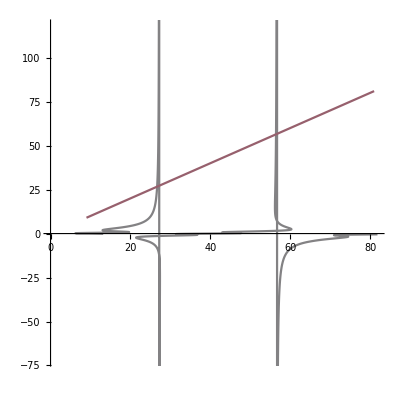

```mathematica
fdata=<|AA->3,BB->9,CC->7|>;
StillPlot["ParametricPlot",{{5Sin[CC x]+x^2,Tan[x]},{x^2,x^2}},{x,AA,BB},fdata,{AspectRatio->1,ColorFunction->"Rainbow"}]
```

```mathematica
ClearAll[TimeAnimation];
TimeAnimation::usage="TimeAnimation[plotfunction,functions,ranges,data,options]
provides a plot of the scalar-valued functionsin such a way that both the functions
and the associated ranges can be specified symbolically (as opposed to numerically).
The imput is as follows:
	\"plotfunction\": Mathematica plot function to use.

	\"functions\": this is a single expression or a list of expressions.
	Each item must be evaluatable numerically once 
		(a) the symbolic parameters are substituted by their values as
			specified in \"data\";
		(b) the ranges for the independent variables are numerically
			resolved, either because they are given sumerically, or
			because they are resolved numerically using the \"data\";
		(c) the independent variables are assigned numerical values in
			their numerically resolved ranges.

	\"ranges\": this is a list or a list of lists specifiying the ranges of
	the independent variables, where time is the last of the independent variables.
	Hence, \"ranges\" has the form {{x,a,b},{y,c,d}, ... {t,t1, t2}},
	where x, y, ..., t are the independent variables in \"functions\".
	NOTE: THE TIME RANGE MUST BE THE LAST RANGE PROVIDED.

	\"data\": this is an association which will be used as a replacement rule
	for any symbols appearing in \"functions\" and \"ranges\".

	\"options\": this is a list of options for the specified \"plotfunction\".";
TimeAnimation::invarg11="The first argument must be a string with the name of a valid Mathematica plotting function.";
TimeAnimation::invarg12="The first argument is not the name of a valid Mathematica plotting function.";
TimeAnimation::invarg2="The second argument must be function that can be numerically evaluated using the \"data\".";
TimeAnimation::invarg31="The third argument must be a list of ranges for the plot coordinates used following the standard syntax in Mathematica, e.g., {{x,0,L},{y,A,B}}. The list may be symbolic but it must result in a numerical range for each variable upon substitution of the \"data\".";
TimeAnimation::invarg32="The list \"ranges\" is not a valid list of ranges.";
TimeAnimation::invarg4="The fourth input must be an association containing the data necessary to numerically evaluate the given function and variable ranges.";
TimeAnimation::invarg5="The fifth argument is a list of options that are meaningful for the Mathematica plot function used.";
TimeAnimation[pf_,f_,r_,data_,options_:{}]:=Module[{SRanges,TRange,TmpV,TmpR},
If[!StringQ@pf,
Message@TimeAnimation::invarg11;
Return@$Failed;
];
If[!NameQ[pf],
Message@TimeAnimation::invarg12;
Return@$Failed;
];
If[!ListQ@r,
Message@TimeAnimation::invarg31;
Return@$Failed;
];
If[Depth@r≠3,
Message@TimeAnimation::invarg32;
Return@$Failed;
];
If[!AllTrue[r,Length@#==3&],
Message@TimeAnimation::invarg32;
Return@$Failed;
];
(* Isolate the space and time ranges. *)
SRanges=Drop[r,-1];
TRange=Last@r;
(* Check that the data have the proper format *)
If[!AssociationQ@data,
Message@TimeAnimation::invarg4;
Return@$Failed;
];
(* Create a test replacement rule for evaluating the given function, and then evaluate the given function. *)
TmpR=#[[1]]->(#[[2]]+#[[3]])/2&/@r/.data;
TmpV= N@Flatten@{(f/.data/.TmpR)};
(* Now check that the test value of the given function is a number. *)
If[!AllTrue[TmpV,NumberQ],
Message@TimeAnimation::invarg2;
Return@$Failed;
];
If[!ListQ@options,
Message@TimeAnimation::invarg5;
Return@$Failed;
];
(* At this point we should be able to produce the plot. *)
Return[Animate[ToExpression[pf][Evaluate[f/.data],Evaluate[Sequence@@(SRanges/.data)],Evaluate[Sequence@@options]],Evaluate[TRange/.data]]
]
];
```

```mathematica
fdata=<|AA->3,BB->9,CC->7,to->10|>;
TimeAnimation["Plot3D",Sin[CC x y  + t]+y Cos[t+x],{{x,AA,BB},{y,BB,CC},{t,0,to}},fdata,{AspectRatio->1,ColorFunction->"Rainbow"}]
```

## Postprocessing Functions

## Usage Manual

## Basic Information

To formulate a FEM problem, the first step is to choose the problem context in terms of problem dimension, and type.  Also, one needs to decide whether or not the problem is time dependent. As far as coordinate systems are concerned, the coordinate system will always be Cartesian except for axisymmetric problem.  With this in mind, the symbols to use for the coordinates can be selected by the use.  The default symbols are (x,y,z) for the Cartesian coordinate system and (r,θ,z) for the cylindrical coordinate system. An additional chioice concerns the naming convection for vector and tensor-valued quantities.

## Field declaration: how to set up the creation of a field with given properties

In this notebook a field is instantiated by using appropriate instantiation functions.  The main argument of these functions is a list that described the properties of the field to be instantiated. We call such a list a field declaration list and it has three entries:

A string with the field’s name: this argument is mandatory.

An integer representing the tensorial order of the field: this argument is mandatory.

An “association” with properties of the field. This argument is optional and the type of properties that are allowed depends on the nature of the field. To facilitate the specification of the properies of the field, these properties are prescribed as a key-value combination.  Examples will be given on a case by case basis.

Here are a few examples:

#### Declaration of a scalar field

Let u be a scalar field as could be the main unknown in the classical form of the Laplace equation. Then the field declaration for the this field is simply

```mathematica
{"u",0}
```

where the tensorial order zero indicates that u is a scalar valued function. As mentioned above, the field declaration list has three parts, the last one being a list in itself that allows to specify some properties of the field, if appropriate.  In the case of scalar fields, the third element of the declaration can be omitted because it is always ignored.

#### Declaration of a vector field

Let u be a vector field as could be the main unknown in the classical form of the linear elastostatic problem, namely, the displacement field. Then the field declaration for the this field is simply

```mathematica
propertiesofu=<|
"Principal Unknown"->false,
"Vector: 2D Formulation Constant Value"->7
|>;
```

```mathematica
{"u",1,propertiesofu}
```

where the tensorial order 1 indicates that u is a vector valued function. With the obove in mind, if the problem is planar or axisymmetric, the components of the vector in the z or θ directions, respectively, are set to zero by default.  If a value different from zero is desired, then, the field declaration should be set to

```mathematica
{"u",1,{value}}
```

where “value” is the prescribed value in in question.  For a vector field, the property entry of the list is ignored in 3D problems.

## Functions and their usage

#### Instantiation of the primary unknown fields

The primary unknown fields are instantiated by evaluating the command

```mathematica
PrimaryFieldsInstantiation[Fields];
```

The variable “Fields” is a list of the field declarations as specificed above (“Fields” is a list of lists).

#### Instantiation of a field that is not a primary unknown

Some equations have source fields in them, such as body forces or mass sources.  In this case, one needs to create the needed source field.

A single source fields is created via the function

```mathematica
FieldInstantiation[f]
```

where f is the field declaration list.

```mathematica
COMSOLExport[MSVariablesFile,"MSJ","Scalar",Coordinates,mdim];
```

```mathematica
MSFieldInstantiation["MSu",uo {Cos[π(x+y)/(4L)],y/L,z/L}];
```

Generated Fields: MSu, DMSu , MSut, MSui, and MSuti.

```mathematica
Data=Union[Data,{L->1Meter,Mh->1Meter}];
```

Union::normal: Nonatomic expression expected at position 1 in Data∪{L→Meter,Mh→Meter}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Data∪{L→Meter,Mh→Meter}.

```mathematica
MSFieldCOMSOLExport[MSVariablesFile,"MSu",1,ProblemSettings];
```

OpenAppend::noopen: Cannot open MSVariablesFile.

WriteString::strml: $Failed is not a string, stream, or list of strings and streams.

General::stop: Further output of WriteString::strml will be suppressed during this calculation.

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

OpenAppend::noopen: Cannot open MSVariablesFile.

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

OpenAppend::noopen: Cannot open MSVariablesFile.

General::stop: Further output of OpenAppend::noopen will be suppressed during this calculation.

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

General::stop: Further output of Close::stream will be suppressed during this calculation.

## Abstract Problem Statement — Weak Form

Consider a regular open set Ω∈ℝ^3 as our physical body, which we model as a non-linear elastic homogeneous and isotropic material.  We denote by Γ the boundary of Ω, oriented by an outward unit normal vector field n_i.  We assume that Γ is partitioned in Dirichlet and Neumann parts, on a component by component basis:

Γ=OverBar[(Γ_g_i∪Γ_h_i)],Γ_g_i∩Γ_h_i=∅.

Let 𝒮_i={u_i|u_i∈H^1(Ω),u_i=g_i on Γ_g_i} and 𝒱_i={w_i|w_i∈H^1(Ω),w_i=0 on Γ_g_i}

Given f_i:Ω→ℝ, g_i:Ω→ℝ, and h_i:Ω→ℝ, and given the constants c_1,c_2 and D_1 of a homogeneous isotropic elastic material, find u_i:Ω̄→ℝ such that, for all w_i∈𝒱_i

π(ϕ̲,J_n,p)=∫_Ω w̄(X,(C̄)_UnderBar[_](ϕ̲,J_n))+p(J(ϕ̲)-Jn)ⅆΩ-∫_Ω f̲.ϕ̲ⅆΩ∫_Γ_h t̄.ϕ̲

where, ϕ̲ is the motion.

Since the energy will be eventually differentiated, we can replace ϕ̲ with the test functions for displacement to obtain the weak form. Thus the potential energy is given as:

π(u̲,J_n,p)=∫_Ω w̄(X,(C̄)_UnderBar[_](u̲,J_n))+p(J(u̲)-Jn)ⅆΩ-∫_Ω w_i f_i ⅆΩ-∑_(i=1)^3 ∫_Γ_h_i w_i h_i ⅆΓ=0

## Formulation

## Problem Settings

### Choice of formulation

The formulation can be one of three types: full 3D, plane strain, or axisymmetric.  Here, we proceed to choose a 2D plane strain, time dependent formulation.

```mathematica
PossibleFormulations={"3D","Plane","Axisymmetric"};
Formulation=PossibleFormulations[[3]];
TimeDependent=True;
```

### Component naming convention for vector and tensor quantities

For fields with components, such as vector or tensor fields, the components of such tensors can be identified by “Numerical” index or an index that reflects the coordinates used.  For example, the components of a velocity vector v can be denoted as {v1,v2,v3} or as {vx,vy,vz} when using coordinates {x,y,z}.  Below, one can select the naming convention, “Numerical” for number and “Coordinates” for that dictated by the coordinates. In all cases, partial dertivatives of a quantities with respect to a coordinate or time will be indicated by the name of the quantity followed by the coordinate in question or time.  That is, if v1 denotes the first component of the vector v, then v1x is the partial derivative of v1 with respect to the coordinate x.  Similarly, v1t is the partial derivative of v1 with respect to time.

```mathematica
ComponentNamingConventionOptions={"Coordinates","Numeric"};
ComponentNamingConvention=ComponentNamingConventionOptions[[1]];
```

### Dimension of the solution’s domain and coordinate system

Being interested in problems motivated by physics, we will posit that these problems are always three dimensional.  With this in mind, there are mathematical formulations of 3D physical problems that have lower dimension.  Here we set the physical dimension of the problem as well as the mathematical dimension of the problem. We denote the physical dimension of a problem by pdim, whereas we denote the dimension of the mathematical formulation by mdim.  Clearly mdim ≤pdim.

#### Standard Consequences — Do not change

```mathematica
pdim=3;
SetAttributes[pdim,{Constant,Protected,ReadProtected}]
```

```mathematica
mdim=Switch[Formulation,"3D",3,"Plane",2,"Axisymmetric",2];
```

#### Coordinate system and outward unit normal — Do not change for consistency with COMSOL

```mathematica
Coordinates=If[Formulation==PossibleFormulations[[3]],{r,phi,z},{x,y,z}];
CoordinateSystem="Cartesian";
If[Formulation==PossibleFormulations[[3]],CoordinateSystem="Cylindrical"];
```

Regardless of the component naming convention, the components of the unit normal are denoted as in COMSOL Multiphysics.

```mathematica
n=ToExpression[("n"<>ToString[#])&/@Coordinates];
```

### Summary of Problem Settings

```mathematica
ProblemSettings=<|"Formulation"->Formulation,"ComponentNaming"->ComponentNamingConvention,"Coordinates"->Coordinates,"CSystem"->CoordinateSystem,"TDependent"->TimeDependent|>;
```

### Initialization of the Formulation Rules and Data Associations — Do not change for Consistency with COMSOL

```mathematica
FormulationRules=<|nphi->0|>;
If[ProblemSettings["Formulation"]=="Plane",FormulationRules=<|nz->0|>];
If[ProblemSettings["Formulation"]=="3D",FormulationRules=<||>];
Data=<||>;
```

## Unknown Fields Instantiation

As a reference, here is the format of the default properties string:

properties = <|
   "Principal Unknown" -> False,
   "Vector: 2D Formulation Constant Value" -> 0,
   "Tensor: 2D Formulation Default Constant Value" -> 0,
   "Tensor: 2D Formulation Address-Value List" -> {},
   "Symmetry" -> "None"
   |>;

### Instantiation setup: field declarations

In this section, we will establish the principal unknowns, their labels, tensor rank, and properties. By default, any initialized field carries with it the properties listed above. To change any of these default settings, identify which property you wish to change and input the new characteristic.

```mathematica
vfDec={"vf",1,<|"Principal Unknown"->True|>};
pfDec={"pf",0,<|"Principal Unknown"->True|>};
umDec={"um",1,<|"Principal Unknown"->True|>};
```

### Fields Instantiations: fields, corresponding test functions, gradients, time rates, and associated replacement rules.

```mathematica
FieldsInstantiation[{vfDec, pfDec, umDec},ProblemSettings];
```

This instantiation updated the FormulationRules and produced the following fields:

{{vf,Tvf,Dvf,TDvf,vft,vftt},{pf,Tpf,Dpf,TDpf,pft,pftt},{um,Tum,Dum,TDum,umt,umtt}}

## Kinematics and/or Constitutive Equations for non dimensional fields

Here are some expressions that are repeatedly used in the weak form:

```mathematica
G = {{g1,0,0}, {0, g1, 0},{0, 0, g3}};
```

```mathematica
Fn[A_?MatrixQ]:=IdentityMatrix[pdim] + uo/Lo A.Inverse[G];
```

```mathematica
Fninv[A_?MatrixQ]:= Inverse[Fn[A]];
```

```mathematica
FninvT[A_?MatrixQ]:= Transpose[Fninv[A]];
```

```mathematica
Jn[A_?MatrixQ] := Det[Fn[A]];
```

## Weak Form

### Weak contribution in the interior of the domain

#### Mesh equations

```mathematica
Jm = FullSimplify[Jn[Leq Dum]//.FormulationRules];
```

```mathematica
umWC = Simplify[Leq^2 IP[TDum.Inverse[G], Dum.Inverse[G] ]//.FormulationRules];
```

#### Fluid equations

```mathematica
Pf = Simplify[Jn[Leq Dum]/Lo(-po pf IdentityMatrix[pdim] + (2 muf vo)/Lo Sym[Leq Dvf.Inverse[G].Fninv[Leq Dum]]).FninvT[Leq Dum].Inverse[Transpose[G]]//.FormulationRules];
```

```mathematica
vfWC = Simplify[Lo/po(Jn[Leq Dum](rhof IP[Tvf, ((vo Leq)/Lo Dvf.Inverse[G].Fninv[Leq Dum].(vo vf - (uo teq)/tau umt) + (vo teq)/tau vft )]) + IP[Leq TDvf, Pf] ) //.FormulationRules];
```

```mathematica
pfWC =Simplify[Jn[Leq Dum] Tpf Tr[Leq Dvf.Inverse[G].Fninv[Leq Dum]]  //.FormulationRules];
```

#### “Pressure” boundary condition

```mathematica
TBCf = Simplify[IP[Tvf, Jn[Leq Dum]FninvT[Leq Dum].Inverse[Transpose[G]].n]//.FormulationRules];
```

#### Particle tracking equations

```mathematica
xcdot = Simplify[Fninv[Leq Dum].(vo vf - uo/tau teq umt)//.FormulationRules];
```

#### Volumetric flow rate

```mathematica
flow = Simplify[vo IP[n,(Lo/Leq)^2 Det[G]Jn[Leq Dum]Inverse[G].Fninv[Leq Dum].vf]//.FormulationRules];
zflow = Simplify[vo IP[{0,0,1},(Lo/Leq)^2 Det[G]Jn[Leq Dum]Inverse[G].Fninv[Leq Dum].vf]//.FormulationRules];
```

#### Energy dissipation rate

```mathematica
epsDot = Simplify[(vo Lo^3/Leq^3 Det[G])IP[Pf, Leq Dvf]//.FormulationRules];
```

## Formulation Output: COMSOL Format

## Reminder of Function Usage in this Chapter

## Set Output Path to the Current Local Directory

```mathematica
OutputPathRoot=NotebookDirectory[];
```

## Set Base Name of Output Files

```mathematica
OutputBaseName=OutputPathRoot<>"NS-ALE-AS";
VariablesFile=OutputBaseName<>"FormulationVariables.txt";
```

## Initialize the Output Files

```mathematica
InitializeOutputFiles[{VariablesFile}];
```

## Detailed Output

### Export: formulation

```mathematica
COMSOLExport[VariablesFile,COMSOLDef["Jm",0,Jm,ProblemSettings]];
COMSOLExport[VariablesFile,COMSOLDef["umWC",0,umWC,ProblemSettings]];
```

```mathematica
COMSOLExport[VariablesFile,COMSOLDef["Pf",2,Pf,ProblemSettings]];
COMSOLExport[VariablesFile,COMSOLDef["vfWC",0,vfWC,ProblemSettings]];
COMSOLExport[VariablesFile,COMSOLDef["pfWC",0,pfWC,ProblemSettings]];
COMSOLExport[VariablesFile,COMSOLDef["TBCf",0,TBCf,ProblemSettings]];
```

```mathematica
COMSOLExport[VariablesFile,COMSOLDef["xcdot",1,xcdot,ProblemSettings]];
```

```mathematica
COMSOLExport[VariablesFile,COMSOLDef["flow",0,flow,ProblemSettings]];
COMSOLExport[VariablesFile,COMSOLDef["zflow",0,zflow,ProblemSettings]];
```

```mathematica
COMSOLExport[VariablesFile,COMSOLDef["epsDot",0,epsDot,ProblemSettings]];
```